# Log analysis 202310-202312

## Title: CiNiiのログから見るユーザーアクセスグラフの計量分析

```mathematica
start=Now
```

Fri 1 Mar 2024 14:47:31GMT+9

### 情報知識学会抄録

log-analysis_W _ 20231001-20231007_vocgr _JSIK2.nb

## コンセプト

アクセスログから分離したユーザーごとのアクセスグラフを一種のプロダクトとみなし、計量書誌学の観点から分析を行う。

用語：
アクセス：ログのアクセスURL
（アクセス）連鎖：リファラー -> アクセスURLとなる”エッジ”およびエッジが連なった”経路”または”グラフ” => グラフの場合はReferrer Graph[1] というらしい。
ユーザーアクセスグラフ：単一ユーザー（推定）によるアクセスのグラフ
ボキャブラリ：アクセスの性質・アクションを端的に表す単語

分析項目の候補：

ユーザーアクセスグラフの規模クラス内のメンバの分布（Zipを仮定）、1日/1週間/3ヶ月

クラスのメンバ数の分布が対象になるのでクラスを作る。（例：被引用が1件のクラス）

vertex数クラス

edge数クラス

ユーザーの特徴的な行動

リファラーと離脱次のURLのボキャブラリ

ボキャブラリ“detail”が付与される、タイムライン内のノードの位置

ユーザーアクセスグラフの類型

プロパティ：voc出現（重み付き/重みなし）

プロパティ：vocによるアクセスグラフ（重み付き/重みなし）のスペクトル

非対称行列（隣接行列そのまま）のスペクトル

キルヒホフ行列のスペクトル（undirectedの場合重みなしとなる）

N次の連鎖

アクセスグラフの類型ごとのメンバー数がZip型分布に従うか？

アクセスグラフの類型をクラスタリングし類型間の関係を確認する

クラスタリング法は？使用する類型のプロパティは？

分析を組み合わせ、各々の類型がどのような行動パターンか説明可能か？

離脱時のURL(voc)/初回アクセスのリファラー（vocがついていないものあり）

どのくらいのユーザーが”detail”まで確認しているか？

NIIサービス連携がどのくらいあるか？

滞留時間は精度がよくないので発表としては使わない？

タイトル：「CiNiiのログから見るユーザーアクセスグラフの計量分析」

参照：

1. B. de la Ossa, A. Pont, J. Sahuquillo, J. A. Gil ; “Referrer graph: a low-cost web prediction algorithm” ; Proceedings of the 2010 ACM Symposium on Applied ComputingMarch 2010Pages 831–838 ; https://doi.org/10.1145/1774088.1774260

```mathematica
Grid[Import["/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/analysis_items.xlsx"][[1]],ItemSize->Full,Frame->All]
```

CiNiiのログから見るユーザーアクセスグラフの計量分析 |  |  |  |  |  |  |  |  |  |  |  |  | 
分析項目の整理 |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 分析項目→ | ユーザーアクセスグラフの構成 | グラフの規模 | voc[detail]のグラフ内の位置 | リファラーと離脱時のアクセスURL(voc) | グラフのN次の連鎖パス | グラフに出現するvocのリスト | vocグラフスペクトル | 滞在/滞留時間 | 連携アクセス |  | [今後]キーワード分析 | [間に合うか？]グラフ使わないクロス集計
 | 目的→ | 分析の基本となるグラフを構成する | グラフの規模の分布を確認する | ・ユーザーがdetailページに辿り着いているか | ・各グラフにおける典型的な行動を捉える | ・各グラフにおける典型的な行動を捉える
・パスの規模の分布を確認する | ・グラフを類型化する
・グラフ類型のクラスタリング
・グラフ類型の規模の分布を確認する | ・グラフを類型化する
・グラフ類型のクラスタリング
・グラフ類型の規模の分布を確認する |  | ・ciと他基盤の連携グラフがどの程度あるか |  |  | 
 | コメント→ |  |  |  |  |  | 0/1出現を利用してクラスを決定
クラスを対象としてクラスタリング | グラフの固有値列を用いてクラスを決定
クラスを対象としてクラスタリング |  |  |  |  | ・リファラーと...
・組織と...
 | グラフタイプ↓/グラフから何を確認すれば良いか→ |  |  |  |  |  |  |  |  |  |  |  | 
 | Basic-graph
リファラー -> アクセスURLの連鎖による有向グラフ | グラフを構成 | - | - | - | - | - | - |  | - |  |  | 
 | voc-label-graph
上記のグラフのvertexにvocを付与したもの | Basic-graphからvoc-label-graphを構成 | ・Vertex
・Edge | ・グラフ内のvertexを最終アクセス時刻順に並べてdetailがどの位置にあるか | ・グラフ内の最初のリファラー
・グラフ内で最後にアクセスしたURL | ・最大連鎖長をグラフごとに取る
・1次（Vertex）
・2次（Edge）
・3次
・何次まで？ | ・重みつきvocリスト
・重みなしvocリスト | - | ・滞留時間：グラフ内vertexのアクセス時刻のMaxとMinの差
・滞在時間：グラフ内vertexをアクセス時刻順に並べ時間間隔を算出したもの | ・条件付きエッジ（リファラーもしくはリクエストURLのvocがci以外を含む、かつciを含む） |  |  | 
 | voc-graph
上記のグラフのvertexをすべてvocに振り直してシュリンクさせたもの | Basic-graphからvoc-graphを構成 | - |  | - | - | - | ・キルヒホフグラフの固有値列 |  | - |  |  | 
 | Saveの対象
(N)

保存先ファイル | ・voc-label-graph
・voc-graph（3種）
(N=グラフ数)

保存先はそれぞれ分ける | ・VertexList
・EdgeList
・Vertex数
・Edge数
(N=グラフ数)

一つのファイル | ・vocが"detail"であるposition <= VertexListとして保存
(N=グラフ数)

左と同じファイル | ・各グラフの最初のリファラーと最後のアクセスURLのペア <= VertexListとして保存
・上記に対するvoc <= VertexListとして保存
(N=グラフ数)

左と同じファイル | ・[保留]voc-label-graphのlongest-path
(N=グラフ数)

保存しない | ・重みつきvoc出現リスト(要素数固定ベクトル)
・重みなしvoc出現リスト(要素数固定ベクトル)
(N=グラフ数)

一つのファイル | ・キルヒホフ行列
・キルヒホフ行列の固有値列
(N=グラフ数)

一つのファイル | ・グラフ滞留時間(一つの値)：グラフ内vertexのアクセス時刻のMaxとMinの差
・ページ滞在時間(リスト)：グラフ内vertexをアクセス時刻順に並べ時間間隔を算出したもの

一つのファイル |  |  |  |

## Target ID

```mathematica
tID=1
```

1

## Basic Program

### vertexにaccess時刻を付与する

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

### access時刻よりあとのreferer-accessを持つEdgeをテストする/落とす

```mathematica
timeEdgeTest[e_]:=Module[{sourceNode,sourceTime,edgeTime,trueCountTest,sourceNodeTest},
sourceNode=e[[1]];
sourceTime=e[[1]][[2]];
edgeTime=e[[3]][[1]];
trueCountTest=Length[Select[edgeTime-sourceTime,#>=0&]]>=1;
sourceNodeTest=Head[sourceNode]===String;
(*{trueCountTest,sourceNodeTest};*);
trueCountTest||sourceNodeTest
]
```

```mathematica
timeGraphTest[g_]:=Module[{el},
el=EdgeList[g];
Map[timeEdgeTest,el]
]
```

```mathematica
timeoutEdgeDelete[g_Graph]:=Module[{el,test,deletePosition},
el=EdgeList[g];
test=Map[timeEdgeTest,el];
deletePosition=Position[test,False];
Graph[Delete[el,deletePosition],VertexLabels->"Name",EdgeLabels->"EdgeTag"]
]
```

```mathematica
??WeaklyConnectedGraphComponents
```

```mathematica
timeoutGraphSplit[g_Graph]:=WeaklyConnectedGraphComponents[timeoutEdgeDelete[g]]
```

### graphからedgeの時刻を抽出

```mathematica
edgeTimeList[gIdx_]:=Map[#[[3,1]]&,EdgeList[gIdx]]
```

### 1回以上のカウントを1とする

```mathematica
exist[0]:=0
exist[a_/;a>0]:=1
```

### 予約

```mathematica
Protect[undefined]
```

{undefined}

## Settings

```mathematica
basedir="/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/

```mathematica
datadir=basedir<>"D=*/T=4/_story/"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=*/T=4/_story/

```mathematica
files=FileNames[datadir<>"storyGrIdxFlDs3*save"]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/storyGrIdxFlDs3.20231001.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/storyGrIdxFlDs3.20231002.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/storyGrIdxFlDs3.20231003.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/storyGrIdxFlDs3.20231004.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/storyGrIdxFlDs3.20231005.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/storyGrIdxFlDs3.20231006.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/storyGrIdxFlDs3.20231007.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231008/T=4/_story/storyGrIdxFlDs3.20231008.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231009/T=4/_story/storyGrIdxFlDs3.20231009.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231010/T=4/_story/storyGrIdxFlDs3.20231010.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231011/T=4/_story/storyGrIdxFlDs3.20231011.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231012/T=4/_story/storyGrIdxFlDs3.20231012.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231013/T=4/_story/storyGrIdxFlDs3.20231013.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231014/T=4/_story/storyGrIdxFlDs3.20231014.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231015/T=4/_story/storyGrIdxFlDs3.20231015.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231016/T=4/_story/storyGrIdxFlDs3.20231016.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231017/T=4/_story/storyGrIdxFlDs3.20231017.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231018/T=4/_story/storyGrIdxFlDs3.20231018.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231019/T=4/_story/storyGrIdxFlDs3.20231019.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231020/T=4/_story/storyGrIdxFlDs3.20231020.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231021/T=4/_story/storyGrIdxFlDs3.20231021.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231022/T=4/_story/storyGrIdxFlDs3.20231022.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231023/T=4/_story/storyGrIdxFlDs3.20231023.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231024/T=4/_story/storyGrIdxFlDs3.20231024.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231025/T=4/_story/storyGrIdxFlDs3.20231025.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231026/T=4/_story/storyGrIdxFlDs3.20231026.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231027/T=4/_story/storyGrIdxFlDs3.20231027.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231028/T=4/_story/storyGrIdxFlDs3.20231028.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231029/T=4/_story/storyGrIdxFlDs3.20231029.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231030/T=4/_story/storyGrIdxFlDs3.20231030.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231031/T=4/_story/storyGrIdxFlDs3.20231031.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231101/T=4/_story/storyGrIdxFlDs3.20231101.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231102/T=4/_story/storyGrIdxFlDs3.20231102.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231103/T=4/_story/storyGrIdxFlDs3.20231103.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231104/T=4/_story/storyGrIdxFlDs3.20231104.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231105/T=4/_story/storyGrIdxFlDs3.20231105.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231106/T=4/_story/storyGrIdxFlDs3.20231106.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231107/T=4/_story/storyGrIdxFlDs3.20231107.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231108/T=4/_story/storyGrIdxFlDs3.20231108.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231109/T=4/_story/storyGrIdxFlDs3.20231109.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231110/T=4/_story/storyGrIdxFlDs3.20231110.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231111/T=4/_story/storyGrIdxFlDs3.20231111.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231112/T=4/_story/storyGrIdxFlDs3.20231112.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231113/T=4/_story/storyGrIdxFlDs3.20231113.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231114/T=4/_story/storyGrIdxFlDs3.20231114.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231115/T=4/_story/storyGrIdxFlDs3.20231115.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231116/T=4/_story/storyGrIdxFlDs3.20231116.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231117/T=4/_story/storyGrIdxFlDs3.20231117.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231118/T=4/_story/storyGrIdxFlDs3.20231118.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231119/T=4/_story/storyGrIdxFlDs3.20231119.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231120/T=4/_story/storyGrIdxFlDs3.20231120.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231121/T=4/_story/storyGrIdxFlDs3.20231121.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231122/T=4/_story/storyGrIdxFlDs3.20231122.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231123/T=4/_story/storyGrIdxFlDs3.20231123.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231124/T=4/_story/storyGrIdxFlDs3.20231124.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231125/T=4/_story/storyGrIdxFlDs3.20231125.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231126/T=4/_story/storyGrIdxFlDs3.20231126.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231127/T=4/_story/storyGrIdxFlDs3.20231127.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231128/T=4/_story/storyGrIdxFlDs3.20231128.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231129/T=4/_story/storyGrIdxFlDs3.20231129.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231130/T=4/_story/storyGrIdxFlDs3.20231130.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231201/T=4/_story/storyGrIdxFlDs3.20231201.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231202/T=4/_story/storyGrIdxFlDs3.20231202.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231203/T=4/_story/storyGrIdxFlDs3.20231203.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231204/T=4/_story/storyGrIdxFlDs3.20231204.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231205/T=4/_story/storyGrIdxFlDs3.20231205.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231206/T=4/_story/storyGrIdxFlDs3.20231206.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231207/T=4/_story/storyGrIdxFlDs3.20231207.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231208/T=4/_story/storyGrIdxFlDs3.20231208.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231209/T=4/_story/storyGrIdxFlDs3.20231209.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231210/T=4/_story/storyGrIdxFlDs3.20231210.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231211/T=4/_story/storyGrIdxFlDs3.20231211.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231212/T=4/_story/storyGrIdxFlDs3.20231212.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231213/T=4/_story/storyGrIdxFlDs3.20231213.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231214/T=4/_story/storyGrIdxFlDs3.20231214.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231215/T=4/_story/storyGrIdxFlDs3.20231215.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231216/T=4/_story/storyGrIdxFlDs3.20231216.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231217/T=4/_story/storyGrIdxFlDs3.20231217.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231218/T=4/_story/storyGrIdxFlDs3.20231218.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231219/T=4/_story/storyGrIdxFlDs3.20231219.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231220/T=4/_story/storyGrIdxFlDs3.20231220.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231221/T=4/_story/storyGrIdxFlDs3.20231221.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231222/T=4/_story/storyGrIdxFlDs3.20231222.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231223/T=4/_story/storyGrIdxFlDs3.20231223.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231224/T=4/_story/storyGrIdxFlDs3.20231224.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231225/T=4/_story/storyGrIdxFlDs3.20231225.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231226/T=4/_story/storyGrIdxFlDs3.20231226.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231227/T=4/_story/storyGrIdxFlDs3.20231227.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231228/T=4/_story/storyGrIdxFlDs3.20231228.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231229/T=4/_story/storyGrIdxFlDs3.20231229.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231230/T=4/_story/storyGrIdxFlDs3.20231230.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231231/T=4/_story/storyGrIdxFlDs3.20231231.save}

```mathematica
fileDirs=Map[StringReplace[#,RegularExpression["/[^/]*$"]->""]&,files];
```

```mathematica
fileDates=Map[StringSplit[#,{"/","="}][[10]]&,files]
```

{20231001,20231002,20231003,20231004,20231005,20231006,20231007,20231008,20231009,20231010,20231011,20231012,20231013,20231014,20231015,20231016,20231017,20231018,20231019,20231020,20231021,20231022,20231023,20231024,20231025,20231026,20231027,20231028,20231029,20231030,20231031,20231101,20231102,20231103,20231104,20231105,20231106,20231107,20231108,20231109,20231110,20231111,20231112,20231113,20231114,20231115,20231116,20231117,20231118,20231119,20231120,20231121,20231122,20231123,20231124,20231125,20231126,20231127,20231128,20231129,20231130,20231201,20231202,20231203,20231204,20231205,20231206,20231207,20231208,20231209,20231210,20231211,20231212,20231213,20231214,20231215,20231216,20231217,20231218,20231219,20231220,20231221,20231222,20231223,20231224,20231225,20231226,20231227,20231228,20231229,20231230,20231231}

```mathematica
vocdir="/Volumes/home/NII/togo-log/rcoslogs/voc/"
```

/Volumes/home/NII/togo-log/rcoslogs/voc/

## Vars

```mathematica
ExternalEvaluate["Shell","grep ' = ' "<>files[[tID]]<>"|awk '{print $1}'"<>" > "<>fileDirs[[tID]]<>"/math-vars_"<>fileDates[[tID]]]
```

Success[…]

```mathematica
vars[fileDates[tID]]=StringSplit[Import[fileDirs[[tID]]<>"/math-vars_"<>fileDates[[tID]],"String"]]
```

{storyGrIdxFlDs3[4]["20231001"],idxLogLen[4],accessTime[4],accessTime["ci"],accessTime["cs"],accessTime["la"],accessTime["wk"],ckanName,ckanCridAC,ckanCridPLogPos[4],ckanCridRLogPos[4],ckanCridPRLogPos[4],ckanCridPlist,ckanCridRlist,ckanCridPRU,ckanCridPLogPosAC[4],ckanCridRLogPosAC[4],ckanCridPRLogPosAC[4],ckanCridPRACQ}

## Data loading / preprocess

計算カーネルの準備

```mathematica
(*CloseKernels[]*)
```

```mathematica
(*LaunchKernels[4]*)
```

データロード

```mathematica
fileDates[[tID]]
```

20231001

```mathematica
AbsoluteTiming[Get[files[[tID]]];]
```

{24.8245,Null}

vertexにアクセス時刻を付与する：

```mathematica
AbsoluteTiming[(storyGrTS[4][fileDates[[tID]]]=Map[addVertexAccTime[#[[3]]]&,storyGrIdxFlDs3[4][fileDates[[tID]]]])//Length]
```

{96.4819,120791}

## Test / graph-reform / graph-selection

### graph split

```mathematica
Off[timeoutGraphSplit,timeEdgeTest]
```

```mathematica
AbsoluteTiming[(storyGrTSS[4][fileDates[[tID]]]=Map[timeoutGraphSplit,storyGrTS[4][fileDates[[tID]]]])//Length]
```

Part::partd: Part specification https://scholar.google.com/⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{115.655,120791}

```mathematica
(storyGrTSSF[4][fileDates[[tID]]]=Flatten[storyGrTSS[4][fileDates[[tID]]]])//Length
```

121361

最終的に欲しいグラフ分割：

```mathematica
(storyGrSel[4][fileDates[[tID]]]=Select[storyGrTSSF[4][fileDates[[tID]]],EdgeCount[#]>=1&&VertexCount[#]>=2&])//Length
```

121359

ユーザーごとにグラフが形成されていることを期待。
ユーザー推定：ソースIPアドレス+ユーザーエージェント
エッジ：リファラー -> アクセスURL
推定のリスク：
1. 同一ユーザーが異なるユーザーと推定されるリスク
2. 異なるユーザーが同一ユーザーと推定されるリスク

## Basic graph

### Graph

```mathematica
storyGrSel[4][fileDates[[tID]]]//Length
```

121359

```mathematica
storyGrSel[4][fileDates[[tID]]][[2001]]//InputForm
```

Graph[{"https://www.google.co.jp/", {"https://cir.nii.ac.jp/crid/1520573330277293952", 
   {3.905111229*^9}}, {"https://cir.nii.ac.jp/crid/1520573329934437120", {3.905144978*^9}}, 
  {"https://cir.nii.ac.jp/crid/1390001205669809024", {3.905175494*^9}}}, 
 {DirectedEdge["https://www.google.co.jp/", {"https://cir.nii.ac.jp/crid/1520573330277293952", 
    {3.905111229*^9}}, {3.905111229*^9, 7445}], DirectedEdge["https://www.google.co.jp/", 
   {"https://cir.nii.ac.jp/crid/1520573329934437120", {3.905144978*^9}}, {3.905144978*^9, 7446}], 
  DirectedEdge["https://www.google.co.jp/", {"https://cir.nii.ac.jp/crid/1390001205669809024", 
    {3.905175494*^9}}, {3.905175494*^9, 7447}]}, {EdgeLabels -> {"EdgeTag"}, 
  VertexLabels -> {"Name"}}]

## voc data

```mathematica
vocRlFiles=FileNames[vocdir<>"/*.wl"]
```

{/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_wk_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_wk_rl.wl}

```mathematica
vocRlList=Map[Get,vocRlFiles];
```

```mathematica
(vocRl["all:path"]=Apply[Join,vocRlList])//Dimensions
```

{113}

voclistをつくる

```mathematica
voclist=Sort[Union[Join[Map[#[[2]]&,vocRl["all:path"]],{undefined[]}]]]
```

{undefined[],voc[ci:*,authenticate,],voc[ci:*,confirm,detail],voc[ci:*,explore,all],voc[ci:*,export,bib],voc[ci*,export,bib],voc[ci:*,request,api],voc[ci:*,request,rdf],voc[ci:*,request,resourcesync],voc[ci:robot,view,robot.txt],voc[ci:*,search,articles],voc[ci:*,search,books],voc[ci:*,search,data],voc[ci:*,search,dssertations],voc[ci:*,search,projects],voc[ci,*,view,top],voc[ci:*,view,top],voc[cs:*,authenticate,],voc[cs:*,confirm,additional_service],voc[cs:*,confirm,token],voc[cs:*,login,],voc[cs:*,request,api],voc[cs:researcher,confirm,item_list],voc[cs:researcher,develop,cluster],voc[cs:researcher,develop,notebook],voc[cs:researcher,develop,terminal],voc[cs:resercher,develop,rstudio],voc[cs:system,internalsystem_access,],voc[cs:*,view,top],voc[la:*,authenticate,],voc[la:*,login,],voc[la:Management,monitor,],voc[la:*,resister,],voc[la:system,internalsystem_access,],voc[la:*,view,content],voc[la:*,view,course_list],voc[la:*,view,dashboard],voc[la:*,view,profile],voc[la:*,view,top],voc[wk:*,authenticate,],voc[wk:*,export,],voc[wk:Management,confirm,admin],voc[wk:Management,confirm,item],voc[wk:Management,confirm,workflow],voc[wk:robot,view,robot.txt],voc[wk:*,search,],voc[wk:*,search,facet],voc[wk:*,search,setting],voc[wk:system,internalsystem_access],voc[wk:system,internalsystem_access,],voc[wk:*,view,about],voc[wk:*,view,analisys],voc[wk:*,view,detail],voc[wk:*,view,guide],voc[wk:*,view,information],voc[wk:*,view,link_list],voc[wk:*,view,manual],voc[wk:*,view,scheme],voc[wk:*,view,top]}

## voc-label graph

### プログラム

```mathematica
(*addVocLabel[gr_,rl_]:=Module[{vl,vname,vrename,vrenameRl},
(*Print["it may cause StringMatchQ warn."];*)
vl=VertexList[gr];
vname=Map[#[[1]]&,vl];
vrename=(vname/.rl);
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]];
Graph[gr,VertexLabels->vrenameRl]
]*)
```

```mathematica
addVocLabel[gr_,rl_]:=Module[{vl,getvname,vname,vrename,vrenameRl},
(*Print["it may cause StringMatchQ warn."];*)
vl=VertexList[gr];
getvname[v_List]:=v[[1]];
getvname[v_String]:=v;
vname=Map[getvname[#]&,vl];
vrename=(vname/.rl);
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]];
Graph[gr,VertexLabels->vrenameRl]
]
```

```mathematica
vocNodeProp[n_]:=If[Head[n]===List,n[[1]],"Undefined"]
```

```mathematica
vertexLabelList[g_]:=Module[{gs,defg},
gs=ToString[InputForm[g]];
defg=ToExpression[StringReplace[gs,"Graph"->"defGraph"]];
Cases[defg,_voc,Infinity]
]
```

```mathematica
countvoc[vocNodeProp_,voclist_]:=Map[Count[vocNodeProp,#]&,voclist]
```

### 適応

vocラベル付きグラフ*

```mathematica
AbsoluteTiming[(storyVocLGrSel[4,"voc"][fileDates[[tID]]]=Map[addVocLabel[#,vocRl["all:path"]]&,storyGrSel[4][fileDates[[tID]]]])//Length]
```

{46.2753,121359}

```mathematica
storyVocLGrSel[4,"voc"][fileDates[[tID]]][[2001]]//InputForm
```

Graph[{"https://www.google.co.jp/", {"https://cir.nii.ac.jp/crid/1520573330277293952", 
   {3.905111229*^9}}, {"https://cir.nii.ac.jp/crid/1520573329934437120", {3.905144978*^9}}, 
  {"https://cir.nii.ac.jp/crid/1390001205669809024", {3.905175494*^9}}}, 
 {DirectedEdge["https://www.google.co.jp/", {"https://cir.nii.ac.jp/crid/1520573330277293952", 
    {3.905111229*^9}}, {3.905111229*^9, 7445}], DirectedEdge["https://www.google.co.jp/", 
   {"https://cir.nii.ac.jp/crid/1520573329934437120", {3.905144978*^9}}, {3.905144978*^9, 7446}], 
  DirectedEdge["https://www.google.co.jp/", {"https://cir.nii.ac.jp/crid/1390001205669809024", 
    {3.905175494*^9}}, {3.905175494*^9, 7447}]}, {EdgeLabels -> {"EdgeTag"}, 
  GraphLayout -> {"Dimension" -> 2}, VertexLabels -> 
   {"Name", {"https://cir.nii.ac.jp/crid/1390001205669809024", {3.905175494*^9}} -> 
     voc["ci:*,confirm,detail"], {"https://cir.nii.ac.jp/crid/1520573330277293952", 
      {3.905111229*^9}} -> voc["ci:*,confirm,detail"], 
    {"https://cir.nii.ac.jp/crid/1520573329934437120", {3.905144978*^9}} -> 
     voc["ci:*,confirm,detail"], "https://www.google.co.jp/" -> "https://www.google.co.jp/"}}]

### edge count

各グラフのエッジリスト

```mathematica
(storyEdgeLSel[4,"voc"][fileDates[[tID]]]=Map[EdgeList,storyVocLGrSel[4,"voc"][fileDates[[tID]]]])//Length
```

121359

edge数*

```mathematica
(storyEdgeSel[4,"voc-edgecount"][fileDates[[tID]]]=Map[Length,storyEdgeLSel[4,"voc"][fileDates[[tID]]]])//Length
```

121359

エッジ数そのもののZipf分布(N(r)=C r^-a)を「一応」確認する：
aは1~3程度が通常、aが小さいほど均等。aはここから乖離しても構わない。

```mathematica
Remove[a,c];
zipf[r_]:=c r^(-a);
zipffit[4,"graph_edge"][fileDates[[tID]]]=FindFit[Sort[storyEdgeSel[4,"voc-edgecount"][fileDates[[tID]]],#1>#2&],zipf[r],{c,a},r]
```

{c→2825.76,a→0.675535}

```mathematica
zipf[r]/.zipffit[4,"graph_edge"][fileDates[[tID]]]
```

2825.76/r^0.675535

エッジ数クラスのメンバ数のZipf分布(N(r)=C r^-a)を確認する：
aは1~3程度が通常、aが小さいほど均等。

```mathematica
tallysort[4,"voc-edgecount-prod"][fileDates[[tID]]]=Sort[Tally[storyEdgeSel[4,"voc-edgecount"][fileDates[[tID]]]],#1[[2]]>#2[[2]]&]
```

{{1,92439},{2,8080},{3,5480},{4,2562},{5,2192},{6,1379},{7,1213},{8,910},{9,790},{10,636},{11,538},{12,467},{13,447},{14,353},{15,313},{17,287},{16,273},{18,207},{19,203},{20,192},{21,166},{22,155},{23,142},{25,127},{24,114},{26,95},{28,92},{27,84},{30,75},{29,70},{31,70},{32,69},{34,60},{35,54},{39,53},{33,51},{38,51},{36,45},{37,36},{44,35},{45,34},{42,33},{40,33},{41,30},{43,29},{46,25},{50,24},{49,23},{53,21},{52,21},{54,20},{56,18},{55,18},{47,16},{48,15},{76,15},{72,14},{51,13},{64,12},{69,11},{67,11},{60,11},{61,9},{57,9},{65,8},{58,8},{63,8},{62,8},{68,8},{88,7},{80,7},{98,7},{66,7},{91,6},{90,6},{59,6},{81,6},{86,5},{89,5},{85,5},{82,5},{84,5},{74,5},{94,5},{112,5},{79,4},{83,4},{78,4},{96,4},{100,4},{95,4},{101,4},{122,4},{73,4},{92,4},{87,4},{77,3},{93,3},{70,3},{75,3},{288,2},{222,2},{107,2},{106,2},{105,2},{71,2},{123,2},{125,2},{104,2},{118,2},{149,2},{138,2},{164,2},{128,2},{102,2},{151,2},{1281,1},{317,1},{103,1},{146,1},{148,1},{181,1},{302,1},{354,1},{150,1},{220,1},{223,1},{246,1},{636,1},{120,1},{117,1},{450,1},{442,1},{455,1},{205,1},{131,1},{485,1},{486,1},{99,1},{203,1},{1344,1},{335,1},{113,1},{116,1},{127,1},{477,1},{162,1},{201,1},{208,1},{456,1},{458,1},{136,1},{137,1},{306,1},{586,1},{145,1},{126,1},{619,1},{629,1},{186,1},{175,1},{172,1},{292,1},{114,1},{645,1},{174,1},{97,1},{108,1},{110,1},{664,1},{652,1},{1678,1},{3020,1},{270,1},{196,1},{213,1},{111,1},{147,1},{154,1},{348,1},{304,1},{140,1},{124,1},{219,1},{167,1}}

```mathematica
Map[#[[2]]&,tallysort[4,"voc-edgecount-prod"][fileDates[[tID]]]]//Total
```

121359

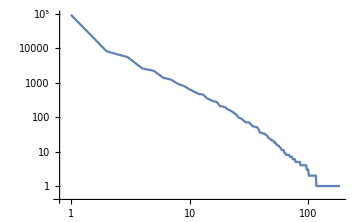

```mathematica
llpe1=ListLogLogPlot[Map[#[[2]]&,tallysort[4,"voc-edgecount-prod"][fileDates[[tID]]]],Joined->True,ImageSize->360]
```

```mathematica
Remove[a,c];
zipf[r_]:=c r^(-a);
zipffit[4,"edge"][fileDates[[tID]]]=FindFit[Map[#[[2]]&,tallysort[4,"voc-edgecount-prod"][fileDates[[tID]]]],zipf[r],{c,a},r]
```

{c→92346.,a→3.20529}

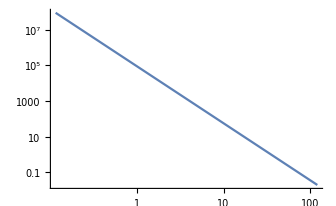

```mathematica
llpe2=LogLogPlot[zipf[r]/.zipffit[4,"edge"][fileDates[[tID]]],{r,0,120},Frame->None,Ticks->None,(*Axes->False,*)ImageSize->336]
```

```mathematica
Overlay[{llpe1,llpe2},Alignment->{1,1}]
```

-Graphics--Graphics-

### vertex count

各グラフのノードリスト*（ラベル情報が落ちる。。。）

```mathematica
(storyNodeLSel[4,"voc"][fileDates[[tID]]]=Map[VertexList,storyVocLGrSel[4,"voc"][fileDates[[tID]]]])//Length
```

121359

vertex数*

```mathematica
(storyNodeSel[4,"voc-nodecount"][fileDates[[tID]]]=Map[Length,storyNodeLSel[4,"voc"][fileDates[[tID]]]])//Length
```

121359

ノード数クラスのメンバ数のZipf分布(N(r)=C r^-a)を確認する：
aは1~3程度が通常、aが小さいほど均等。

```mathematica
tallysort[4,"voc-nodecount-prod"][fileDates[[tID]]]=Sort[Tally[storyNodeSel[4,"voc-nodecount"][fileDates[[tID]]]],#1[[2]]>#2[[2]]&]
```

{{2,96834},{3,9483},{4,3863},{5,2225},{6,1600},{7,1148},{8,893},{9,708},{10,587},{11,472},{12,382},{13,361},{14,286},{15,270},{16,221},{17,187},{18,181},{19,150},{20,136},{21,117},{22,103},{23,92},{26,79},{25,77},{24,75},{27,65},{28,56},{31,49},{30,44},{29,44},{34,36},{32,33},{33,31},{39,27},{36,26},{35,22},{40,21},{38,21},{37,20},{42,19},{43,17},{45,16},{61,14},{48,11},{52,10},{41,10},{46,10},{51,10},{47,9},{53,9},{57,9},{67,8},{49,8},{44,8},{54,7},{68,7},{63,6},{56,6},{55,6},{65,5},{60,5},{66,5},{69,5},{50,5},{90,4},{74,4},{72,4},{70,4},{58,3},{78,3},{82,3},{59,3},{229,2},{334,2},{77,2},{80,2},{85,2},{62,2},{283,2},{98,2},{83,2},{86,2},{87,2},{107,2},{95,2},{121,2},{94,2},{996,1},{285,1},{106,1},{115,1},{139,1},{160,1},{189,1},{170,1},{76,1},{157,1},{99,1},{73,1},{88,1},{262,1},{230,1},{113,1},{1079,1},{299,1},{92,1},{210,1},{114,1},{116,1},{118,1},{91,1},{200,1},{202,1},{96,1},{223,1},{117,1},{273,1},{130,1},{140,1},{396,1},{111,1},{151,1},{101,1},{75,1},{297,1},{288,1},{105,1},{134,1},{108,1},{79,1},{64,1},{259,1},{119,1},{89,1},{132,1},{93,1},{84,1},{135,1}}

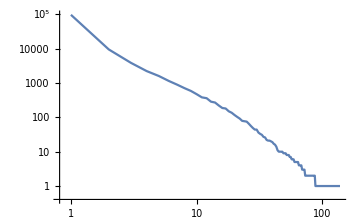

```mathematica
llpn1=ListLogLogPlot[Map[#[[2]]&,tallysort[4,"voc-nodecount-prod"][fileDates[[tID]]]],Joined->True,ImageSize->360]
```

```mathematica
Remove[a,c];
zipf[r_]:=c r^(-a);
zipffit[4,"node"][fileDates[[tID]]]=FindFit[Map[#[[2]]&,tallysort[4,"voc-nodecount-prod"][fileDates[[tID]]]],zipf[r],{c,a},r]
```

{c→96784.7,a→3.21166}

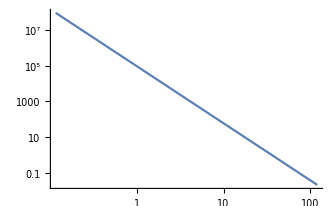

```mathematica
llpn2=LogLogPlot[zipf[r]/.zipffit[4,"node"][fileDates[[tID]]],{r,0,120},Frame->None,Ticks->None,(*Axes->False,*)ImageSize->336]
```

```mathematica
Overlay[{llpn1,llpn2},Alignment->{1,1}]
```

-Graphics--Graphics-

### time-sorted vertex(mintime)

```mathematica
timeSortVLMin[g_]:=Module[{vl,notimeV,timeV},
vl=VertexList[g];
notimeV=Cases[vl,_String];
timeV=Complement[vl,notimeV];
Join[Sort[notimeV],Sort[timeV,Min[#1[[2]]]<Min[#2[[2]]]&]]
]
```

```mathematica
timeSortVLMax[g_]:=Module[{vl,notimeV,timeV},
vl=VertexList[g];
notimeV=Cases[vl,_String];
timeV=Complement[vl,notimeV];
Join[Sort[notimeV],Sort[timeV,Max[#1[[2]]]<Max[#2[[2]]]&]]
]
```

```mathematica
vocDetailReport01[vl_]:=Module[{l,p},
l=Length[vl];
p=Position[vl,voc["ci:*,confirm,detail"]];
{l,Map[#[[1]]&,p]}
]
```

ノードリストの最終アクセス時刻順

```mathematica
(storyNodeLSel[4,"acctimesort"][fileDates[[tID]]]=Map[timeSortVLMax,storyVocLGrSel[4,"voc"][fileDates[[tID]]]])//Length
```

121359

```mathematica
storyNodeLSel[4,"acctimesort"][fileDates[[tID]]][[2008]]
```

{https://cir.nii.ac.jp/all?q=%E9%9D%9E%E8%B2%A1%E5%8B%99%E6%83%85%E5%A0%B1&hasLinkToFullText=true&page=3,{https://cir.nii.ac.jp/crid/1050010488699288832,{3.90519×10^9}},{https://cir.nii.ac.jp/all?q=%E9%9D%9E%E8%B2%A1%E5%8B%99%E6%83%85%E5%A0%B1&hasLinkToFullText=true&hasLinkToFullText=true&count=20&sortorder=0,{3.90519×10^9,3.90519×10^9}},{https://cir.nii.ac.jp/crid/1050855278612397824,{3.90519×10^9}},{https://cir.nii.ac.jp/all?q=%E9%9D%9E%E8%B2%A1%E5%8B%99%E6%83%85%E5%A0%B1&hasLinkToFullText=true&sortorder=0&page=2,{3.90519×10^9,3.90519×10^9}},{https://cir.nii.ac.jp/crid/1390009226273540864,{3.90519×10^9}}}

vocリストの最終アクセス時刻順

```mathematica
AbsoluteTiming[(storyNodeLSel[4,"acctimesort","voc"][fileDates[[tID]]]=Map[ReplaceAll[#,vocRl["all:path"]]&,storyNodeLSel[4,"acctimesort"][fileDates[[tID]]]])//Length]
```

{32.7982,121359}

vocリスト中のdetailの位置*

```mathematica
(vocDetailPos[4][fileDates[[tID]]]=Map[vocDetailReport01,storyNodeLSel[4,"acctimesort","voc"][fileDates[[tID]]]])//Length
```

121359

```mathematica
vocDetailPos[4][fileDates[[tID]]][[2008]]
```

{6,{2,4,6}}

detailに辿り着いていないケースの数

```mathematica
Cases[vocDetailPos[4][fileDates[[tID]]],x_/;x[[2]]=={}]//Length
```

8695

### first-in last-out

```mathematica
firstINlastOUT[g_]:=Module[{vl,notimeV,timeV,minV,maxV},
vl=VertexList[g];
notimeV=Cases[vl,_String];
timeV=Complement[vl,notimeV];
minV=Sort[timeV,Min[#1[[2]]]<Min[#2[[2]]]&][[1]];
maxV=Sort[timeV,Max[#1[[2]]]<Max[#2[[2]]]&][[-1]];
If[notimeV!={},minV=notimeV[[1]]];
{minV,maxV}
]
```

グラフの最初のリファラーと離脱次のURLのペア*

```mathematica
(storyNodePSel[4,"firstANDlast"][fileDates[[tID]]]=Map[firstINlastOUT,storyVocLGrSel[4,"voc"][fileDates[[tID]]]])//Dimensions
```

{121359,2}

グラフの最初のリファラーと離脱次のvocのペア*

```mathematica
dropAcctime[v_]:=Module[{vocnode},
vocnode[n_String]:=n;
vocnode[n_voc]:=n;
vocnode[n_List]:=vocnode[n[[1]]];
vocnode[v]
]
```

```mathematica
dropQuery[v_]:=If[Head[v]===String,StringSplit[v,"?"][[1]],v]
```

```mathematica
domainExtract[v_]:=If[Head[v]===String,StringSplit[v,"/"][[3]],v]
```

```mathematica
AbsoluteTiming[(storyNodePSel[4,"firstANDlast","voc"][fileDates[[tID]]]=Map[ReplaceAll[#,vocRl["all:path"]]&,storyNodePSel[4,"firstANDlast"][fileDates[[tID]]]])//Dimensions]
```

{25.0379,{121359,2}}

```mathematica
(storyNodePSel[4,"firstANDlast","voc","dropAccT"][fileDates[[tID]]]=Map[dropAcctime,storyNodePSel[4,"firstANDlast","voc"][fileDates[[tID]]],{2}])//Dimensions
```

{121359,2}

```mathematica
(storyNodePSel[4,"firstANDlast","voc","dropAccT","domain"][fileDates[[tID]]]=Map[domainExtract,storyNodePSel[4,"firstANDlast","voc","dropAccT"][fileDates[[tID]]],{2}])//Dimensions
```

Part::partw: Part 3 of {porntrex.com} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{121359,2}

In - Out集計

```mathematica
(storyNodeInOutClass[4][fileDates[[tID]]]=Sort[Tally[storyNodePSel[4,"firstANDlast","voc","dropAccT","domain"][fileDates[[tID]]]],#1[[2]]>#2[[2]]&])//Dimensions
```

{1693,2}

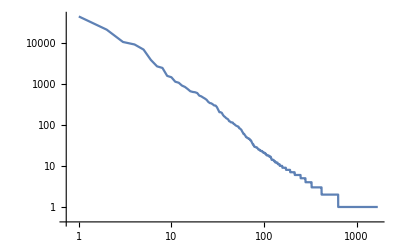

```mathematica
ListLogLogPlot[Map[#[[2]]&,storyNodeInOutClass[4][fileDates[[tID]]]],Joined->True]
```

```mathematica
storyNodeInOutClass[4][fileDates[[tID]]][[1;;100]]
```

{{{ci.nii.ac.jp,voc[ci:*,confirm,detail]},43018},{{www.google.com,voc[ci:*,confirm,detail]},20543},{{www.google.co.jp,voc[ci:*,confirm,detail]},10304},{{search.yahoo.co.jp,voc[ci:*,confirm,detail]},8956},{{scholar.google.com,voc[ci:*,confirm,detail]},6739},{{www.bing.com,voc[ci:*,confirm,detail]},3768},{{scholar.google.co.jp,voc[ci:*,confirm,detail]},2631},{{voc[ci:*,view,top],voc[ci:*,explore,all]},2410},{{voc[ci:*,explore,all],voc[ci:*,explore,all]},1544},{{www.google.com,voc[ci:*,explore,all]},1429},{{voc[ci:*,view,top],voc[ci:*,confirm,detail]},1114},{{voc[ci:*,explore,all],voc[ci:*,confirm,detail]},1051},{{voc[ci:*,confirm,detail],voc[ci:*,confirm,detail]},897},{{search.jamas.or.jp,voc[ci:*,confirm,detail]},831},{{www.google.com,voc[ci:*,view,top]},738},{{ci.nii.ac.jp,voc[ci:*,view,top]},653},{{www.bing.com,voc[ci:*,explore,all]},628},{{voc[ci:*,search,articles],voc[ci:*,search,articles]},617},{{t.co,voc[ci:*,confirm,detail]},591},{{voc[ci:*,confirm,detail],voc[ci:*,explore,all]},511},{{www.google.co.jp,voc[ci:*,explore,all]},491},{{scholar.google.jp,voc[ci:*,confirm,detail]},459},{{iss.ndl.go.jp,voc[ci:*,view,top]},433},{{voc[ci:*,view,top],voc[ci:*,search,articles]},404},{{ci.nii.ac.jp,voc[ci:*,search,articles]},360},{{www.google.co.jp,voc[ci:*,view,top]},337},{{voc[ci:*,search,articles],voc[ci:*,confirm,detail]},331},{{search.yahoo.co.jp,voc[ci:*,explore,all]},313},{{www.google.com,voc[ci:*,search,articles]},294},{{scholar.google.es,voc[ci:*,confirm,detail]},293},{{scholar.google.de,voc[ci:*,confirm,detail]},268},{{www.bing.com,voc[ci:*,search,articles]},232},{{www.wikidata.org,voc[ci:*,confirm,detail]},202},{{search.yahoo.co.jp,voc[ci:*,view,top]},201},{{kaken.nii.ac.jp,voc[ci:*,confirm,detail]},195},{{www.google.com,voc[ci:*,request,resourcesync]},174},{{www.gproxx.com,voc[ci:*,confirm,detail]},161},{{voc[ci:*,explore,all],voc[ci:*,search,articles]},154},{{scholar.google.com.br,voc[ci:*,confirm,detail]},145},{{scholar.google.com,voc[ci:*,explore,all]},140},{{scholar.google.com.au,voc[ci:*,confirm,detail]},135},{{www.bing.com,voc[ci:*,view,top]},122},{{sc.panda321.com,voc[ci:*,confirm,detail]},120},{{scholar.google.com.hk,voc[ci:*,confirm,detail]},114},{{duckduckgo.com,voc[ci:*,confirm,detail]},114},{{service.smt.docomo.ne.jp,voc[ci:*,confirm,detail]},113},{{www.google.co.jp,voc[ci:*,search,articles]},105},{{tripitaka.l.u-tokyo.ac.jp,voc[ci:*,confirm,detail]},103},{{ja.m.wikipedia.org,voc[ci:*,explore,all]},98},{{scholar.google.com.tw,voc[ci:*,confirm,detail]},95},{{ja.m.wikipedia.org,voc[ci:*,confirm,detail]},93},{{ja.wikipedia.org,voc[ci:*,confirm,detail]},91},{{researchmap.jp,voc[ci:*,confirm,detail]},90},{{ci.nii.ac.jp:443,voc[ci:*,view,top]},82},{{search.yahoo.co.jp,voc[ci:*,search,articles]},81},{{cn.bing.com,voc[ci:*,confirm,detail]},78},{{www.google.com.hk,voc[ci:*,confirm,detail]},75},{{nrid.nii.ac.jp,voc[ci:*,confirm,detail]},69},{{scholar.google.co.jp,voc[ci:*,explore,all]},65},{{scholar.google.co.uk,voc[ci:*,confirm,detail]},60},{{websearch.rakuten.co.jp,voc[ci:*,confirm,detail]},60},{{scholar.google.co.kr,voc[ci:*,confirm,detail]},56},{{ja.wikipedia.org,voc[ci:*,explore,all]},54},{{voc[ci:*,confirm,detail],voc[ci:*,search,articles]},50},{{ci.nii.ac.jp,voc[ci:*,explore,all]},50},{{so1.cljtscd.com,voc[ci:*,confirm,detail]},48},{{csweb.ibaraki.ac.jp,voc[ci:*,confirm,detail]},47},{{voc[ci:*,search,articles],voc[ci:*,explore,all]},47},{{kango-sakuin.nurse.or.jp,voc[ci:*,confirm,detail]},45},{{scholar.google.co.id,voc[ci:*,confirm,detail]},45},{{cir.nii.ac.jp,voc[ci:*,confirm,detail]},42},{{www.google.com,voc[ci:*,search,books]},42},{{scholar.google.ca,voc[ci:*,confirm,detail]},40},{{ci.nii.ac.jp:443,voc[ci:*,confirm,detail]},37},{{voc[ci:*,view,top],voc[ci:*,search,books]},35},{{scholar.google.ru,voc[ci:*,confirm,detail]},33},{{altmetrics.ceek.jp,voc[ci:*,confirm,detail]},33},{{sp-web.search.auone.jp,voc[ci:*,confirm,detail]},30},{{m.wikidata.org,voc[ci:*,confirm,detail]},29},{{cn.bing.com,voc[ci:*,explore,all]},29},{{voc[ci:*,view,top],voc[ci:*,search,dssertations]},29},{{www.tulips.tsukuba.ac.jp,voc[ci:*,confirm,detail]},28},{{cir.nii.ac.jp,voc[ci:*,search,articles]},28},{{voc[ci:*,explore,all],voc[ci:*,view,top]},28},{{www.gproxx.com,voc[ci:*,search,books]},27},{{voc[ci:*,request,api],voc[ci:*,search,articles]},26},{{scholar.google.gr,voc[ci:*,confirm,detail]},25},{{scholar.google.fr,voc[ci:*,confirm,detail]},25},{{www.google.com.tw,voc[ci:*,confirm,detail]},25},{{search.jamas.or.jp,voc[ci:*,explore,all]},24},{{so2.cljtscd.com,voc[ci:*,confirm,detail]},24},{{altmetrics.ceek.jp,voc[ci:*,view,top]},23},{{bauddha.dhii.jp,voc[ci:*,confirm,detail]},23},{{opac.dl.itc.u-tokyo.ac.jp,voc[ci:*,confirm,detail]},23},{{voc[ci:*,confirm,detail],voc[ci:*,view,top]},23},{{voc[ci:*,search,books],voc[ci:*,confirm,detail]},22},{{support.nii.ac.jp,voc[ci:*,confirm,detail]},22},{{so3.cljtscd.com,voc[ci:*,confirm,detail]},21},{{support.nii.ac.jp,voc[ci:*,explore,all]},21},{{www.ecosia.org,voc[ci:*,confirm,detail]},21}}

Inのみ集計

```mathematica
(storyNodeInClass[4][fileDates[[tID]]]=Sort[Tally[Map[#[[1]]&,storyNodePSel[4,"firstANDlast","voc","dropAccT","domain"][fileDates[[tID]]]]],#1[[2]]>#2[[2]]&])//Length
```

1166

Outのみ集計

```mathematica
(storyNodeOutClass[4][fileDates[[tID]]]=Sort[Tally[Map[#[[2]]&,storyNodePSel[4,"firstANDlast","voc","dropAccT","domain"][fileDates[[tID]]]]],#1[[2]]>#2[[2]]&])//Length
```

27

```mathematica
storyNodeOutClass[4][fileDates[[tID]]]//TableForm
```

voc[ci:*,confirm,detail] | 106449
voc[ci:*,explore,all] | 8436
voc[ci:*,view,top] | 3082
voc[ci:*,search,articles] | 2665
voc[ci:*,search,books] | 211
voc[ci:*,request,resourcesync] | 174
voc[ci:*,search,dssertations] | 107
voc[la:system,internalsystem_access,] | 91
voc[ci:*,search,data] | 42
cir.nii.ac.jp | 18
voc[ci:*,search,projects] | 16
voc[wk:*,view,top] | 12
voc[wk:system,internalsystem_access] | 11
voc[la:*,view,top] | 8
voc[la:*,authenticate,] | 8
voc[wk:system,internalsystem_access,] | 6
voc[cs:system,internalsystem_access,] | 5
voc[cs:resercher,develop,rstudio] | 4
voc[ci:robot,view,robot.txt] | 2
voc[wk:*,view,detail] | 2
voc[cs:researcher,confirm,item_list] | 2
voc[wk:*,search,] | 2
lms.nii.ac.jp | 2
voc[la:*,view,content] | 1
voc[wk:Management,confirm,item] | 1
jdcat.jsps.go.jp | 1
voc[wk:*,export,] | 1

### N次パス（検討中）

### 可視化（検討中）

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,f];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
timef["Log"][x_]=Log[x+1]
```

Log[1+x]

```mathematica
timef["none"][x_]=x
```

x

Part::partd: Part specification https://cir.nii.ac.jp/all?q=%E9%9D%9E%E8%B2%A1%E5%8B%99%E6%83%85%E5%A0%B1&hasLinkToFullText=true&page=3⟦2⟧ is longer than depth of object.

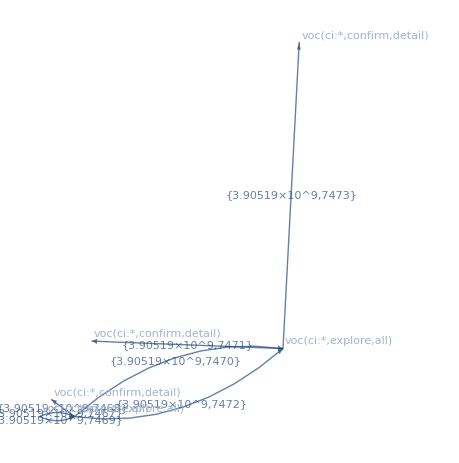

```mathematica
timeLineGr[storyVocLGrSel[4,"voc"][fileDates[[tID]]][[2008]],0,timef["none"]]
```

Part::partd: Part specification https://cir.nii.ac.jp/all?q=%E9%9D%9E%E8%B2%A1%E5%8B%99%E6%83%85%E5%A0%B1&hasLinkToFullText=true&page=3⟦2⟧ is longer than depth of object.

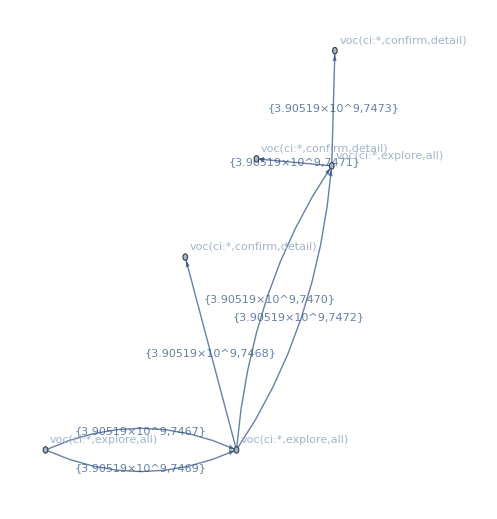

```mathematica
timeLineGr[storyVocLGrSel[4,"voc"][fileDates[[tID]]][[2008]],0,timef["Log"]]
```

Part::partd: Part specification https://www.google.co.jp/⟦2⟧ is longer than depth of object.

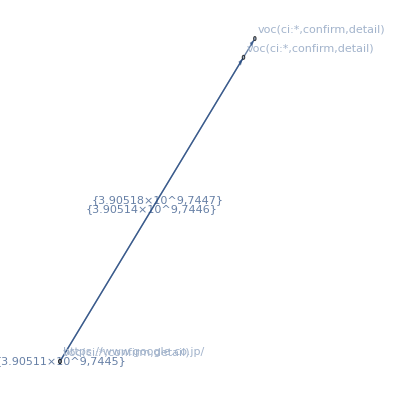

```mathematica
timeLineGr[storyVocLGrSel[4,"voc"][fileDates[[tID]]][[2001]],0,timef["Log"]]
```

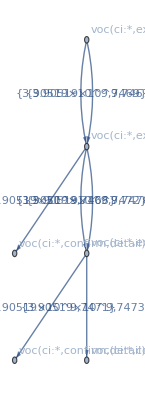

```mathematica
storyVocLGrSel[4,"voc"][fileDates[[tID]]][[2008]]
```

### voc vector

各グラフのvocリスト(vocが振られたものだけ抽出)

```mathematica
AbsoluteTiming[(storyVocNodeSel[4,"voc-only"][fileDates[[tID]]]=Map[vertexLabelList,storyVocLGrSel[4,"voc"][fileDates[[tID]]]])//Length]
```

{35.8965,121359}

重み付きvoc出現リスト*

```mathematica
(storyVocCVecSel[4,"voc-only"][fileDates[[tID]]]=Map[countvoc[#,voclist]&,storyVocNodeSel[4,"voc-only"][fileDates[[tID]]]])//Length
```

121359

重みなし(0/1)voc出現リスト*

```mathematica
(storyVocAVecSel[4,"voc-only"][fileDates[[tID]]]=Map[exist,storyVocCVecSel[4,"voc-only"][fileDates[[tID]]],{2}])//Length
```

121359

Tallyでクラスを作る

```mathematica
classSize=(storyVocAVecClass[4,"voc-only"][fileDates[[tID]]]=Sort[Tally[storyVocAVecSel[4,"voc-only"][fileDates[[tID]]]],#1[[2]]>=#2[[2]]&])//Length
```

198

```mathematica
storyVocAVecClass[4,"voc-only"][fileDates[[tID]]][[1]]
```

{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},97698}

### voc vectorクラスタリング

クラスタリング前の分布の確認

```mathematica
Map[#[[1]]&,storyVocAVecClass[4,"voc-only"][fileDates[[tID]]]]//Dimensions
```

{198,59}

```mathematica
(storyVocAVecClassPCA[4,"voc-only"][fileDates[[tID]]]=PrincipalComponents[    N[Map[#[[1]]&,storyVocAVecClass[4,"voc-only"][fileDates[[tID]]]]]    ])//Dimensions
```

{198,59}

```mathematica
(point3D=Map[#[[1;;3]]&,storyVocAVecClassPCA[4,"voc-only"][fileDates[[tID]]]])//Dimensions
```

{198,3}

```mathematica
Graphics3D[Map[Point,point3D]]
```

-Graphics3D-

クラスを階層クラスタリング（出現ベクトル）

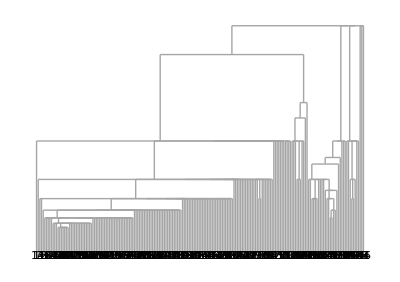

```mathematica
Dendrogram[  Map[#[[1]]&,storyVocAVecClass[4,"voc-only"][fileDates[[tID]]]]  ->Table[n,{n,classSize}]]
```

vocを階層クラスタリング（出現ベクトル）

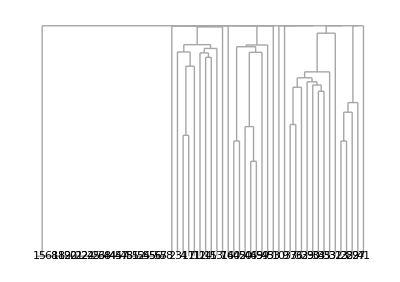

```mathematica
Dendrogram[Transpose[storyVocAVecSel[4,"voc-only"][fileDates[[tID]]]]->Table[n,{n,Length[voclist]}]]
```

### 滞留時間

```mathematica
(edgeAccTimeList[4][fileDates[[tID]]]=Map[edgeTimeList,storyVocLGrSel[4,"voc"][fileDates[[tID]]]])//Dimensions
```

{174420}

```mathematica
(edgeAccTimeList[4,"stay"][fileDates[[tID]]]=Map[Max[#]-Min[#]&,edgeAccTimeList[4][fileDates[[tID]]]])//Dimensions
```

{174420}

### ページ滞在時間（取得できないものは0としている）

```mathematica
visitTime[tl_]:=Module[{sorted,parted},
sorted=Sort[tl,#1>#2&];
parted=Partition[sorted,2,1];
Map[#[[1]]-#[[2]]&,parted]
]
```

```mathematica
(edgeAccTimeList[4,"pagevisit"][fileDates[[tID]]]=((Map[visitTime,edgeAccTimeList[4][fileDates[[tID]]]])/.{}->0))//Length
```

174420

## voc graph

URLをvocにreplaceしたグラフを作る。

最終的にキルヒホフグラフを作る。

### プログラム

```mathematica
toVocGraph[gr_,rl_]:=Module[{el},
el=EdgeList[gr];
Graph[el/.rl,VertexLabels->"Name"]
]
```

```mathematica
dropAcctimeFromEdge[e_]:=Module[{dropAcctime,h},
h=Head[e];
dropAcctime[n_List]:=If[Head[n[[1]]]===voc,n[[1]],undefined[]];
dropAcctime[n_voc]:=n;
dropAcctime[n_String]:=undefined[];
(*h[dropAcctime[e[[1]]],dropAcctime[e[[2]]],e[[3]]];*)
h[dropAcctime[e[[1]]],dropAcctime[e[[2]]]]
]
```

```mathematica
dropAcctimeFromEdgeUD[e_]:=Module[{dropAcctime,h},
h=Head[e];
dropAcctime[n_List]:=If[Head[n[[1]]]===voc,n[[1]],undefined[]];
dropAcctime[n_voc]:=n;
dropAcctime[n_String]:=undefined[];
(*UndirectedEdge[dropAcctime[e[[1]]],dropAcctime[e[[2]]],e[[3]]];*)
UndirectedEdge[dropAcctime[e[[1]]],dropAcctime[e[[2]]]]
]
```

```mathematica
dropAcctimeFromGraph[g_Graph]:=Module[{el},
el=EdgeList[g];
Graph[Map[dropAcctimeFromEdge,el]]
]
```

```mathematica
dropAcctimeFromGraph[g_Graph,vl_]:=Module[{el},
el=EdgeList[g];
Graph[vl,Map[dropAcctimeFromEdge,el]]
]
```

```mathematica
dropAcctimeFromGraphUD[g_Graph]:=Module[{el},
el=EdgeList[g];
Graph[Map[dropAcctimeFromEdgeUD,el]]
]
```

```mathematica
dropAcctimeFromGraphUD[g_Graph,vl_]:=Module[{el},
el=EdgeList[g];
Graph[vl,Map[dropAcctimeFromEdgeUD,el]]
]
```

### 適応

アクセス時刻付き有向vocグラフ*

```mathematica
AbsoluteTiming[(storyVocGraphSel[4][fileDates[[tID]]]=Map[toVocGraph[#,vocRl["all:path"]]&,storyGrSel[4][fileDates[[tID]]]])//Length]
```

{144.399,121359}

アクセス時刻なし有向vocグラフ

```mathematica
AbsoluteTiming[(storyVocGraphDASel[4][fileDates[[tID]]]=Map[dropAcctimeFromGraph,storyVocGraphSel[4][fileDates[[tID]]]])//Length]
```

{10.5575,121359}

アクセス時刻なし無向vocグラフをつくる準備

```mathematica
AbsoluteTiming[(storyVocGraphDAUDSel[4][fileDates[[tID]]]=Map[dropAcctimeFromGraphUD,storyVocGraphSel[4][fileDates[[tID]]]])//Length]
```

{10.4481,121359}

```mathematica
AbsoluteTiming[(storyVocGraphDAUDSel59ex[4][fileDates[[tID]]]=Map[dropAcctimeFromGraphUD[#,voclist]&,storyVocGraphSel[4][fileDates[[tID]]]])//Length]
```

{12.6797,121359}

```mathematica
(storyVocGraphDAUDSel59ex[4,"vcount"][fileDates[[tID]]]=Map[VertexCount,storyVocGraphDAUDSel59ex[4][fileDates[[tID]]]]);
```

vocがマップしきれていない場合除外でよいか。。。

アクセス時刻なし無向vocグラフ*

```mathematica
(storyVocGraphDAUDSel59[4][fileDates[[tID]]]=Cases[storyVocGraphDAUDSel59ex[4][fileDates[[tID]]],x_/;VertexCount[x]==59])//Dimensions
```

{121359}

キルヒホフ行列*

```mathematica
AbsoluteTiming[(storyVocGraphKM59[4][fileDates[[tID]]]=Map[KirchhoffMatrix,storyVocGraphDAUDSel59[4][fileDates[[tID]]]])//Dimensions]
```

{17.9942,{121359,59,59}}

キルヒホフ行列の固有値列*

```mathematica
(storyVocGraphEva59[4][fileDates[[tID]]]=Map[Eigenvalues[N[#]]&,storyVocGraphKM59[4][fileDates[[tID]]]])//Dimensions
```

{121359,59}

### 固有値によるクラスタリング

Tallyでクラスをつくる

```mathematica
(storyVocGraphEva59Class[4][fileDates[[tID]]]=Tally[storyVocGraphEva59[4][fileDates[[tID]]]])//Dimensions
```

{800,2}

```mathematica
EvaClassSize=Length[storyVocGraphEva59Class[4][fileDates[[tID]]]]
```

800

クラスのベクトル集合のPCA

```mathematica
(storyVocGraphEva59ClassPCA[4][fileDates[[tID]]]=PrincipalComponents[N[Map[#[[1]] &, storyVocGraphEva59Class[4][fileDates[[tID]]]]]])//Dimensions
```

{800,59}

```mathematica
storyVocGraphEva59Class[4][fileDates[[tID]]][[1]]
```

{{2.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},104311}

```mathematica
storyVocGraphEva59ClassPCA[4][fileDates[[tID]]][[1]]
```

{4.42088,0.89841,1.58897,0.555258,0.104242,0.027862,0.00102411,0.0119618,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

分布確認

```mathematica
Eva59Point=Map[Point[#[[1;;3]]]&,storyVocGraphEva59ClassPCA[4][fileDates[[tID]]]];
```

```mathematica
Graphics3D[Eva59Point]
```

-Graphics3D-

クラスタリング

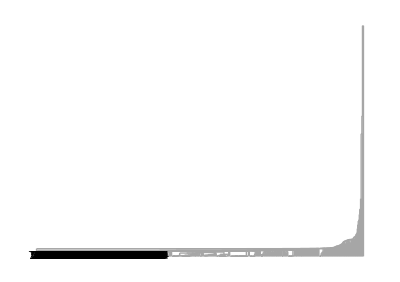

```mathematica
Dendrogram[N[Map[#[[1]]&,storyVocGraphEva59Class[4][fileDates[[tID]]]]]->Table[n,{n,EvaClassSize}]]
```

## Graph selection 行うか？

異なるユーザーが同一ユーザーと推定されるリスクを減らす。

A. このリスクが高い場合、ページの滞在時間が短く計測されるはず
　-> ページ滞在時間の平均が一定以上のグラフを選択する。

B. このリスクが高い場合、閲覧ページ数（グラフにおけるノード数）が極端に高くなるはず
　-> ノード数が一定以下のグラフを選択する。

## Save

voc-label-graph

```mathematica
vocLGraphSaveFile=fileDirs[[tID]]<>"/log-analysis_"<>fileDates[[tID]]<>"_vocLGraph.save"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_vocLGraph.save

```mathematica
(*AbsoluteTiming[Save[vocLGraphSaveFile,storyVocLGrSel]]*)
```

voc-graph

```mathematica
vocGraphSaveFile=fileDirs[[tID]]<>"/log-analysis_"<>fileDates[[tID]]<>"_vocGraph.save"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_vocGraph.save

```mathematica
(*AbsoluteTiming[Save[vocGraphSaveFile,{storyVocGraphSel,storyVocGraphDAUDSel59}]]*)
```

edge+vertex count, detail-page position

```mathematica
EVcountSaveFile=fileDirs[[tID]]<>"/log-analysis_"<>fileDates[[tID]]<>"_EVcount.save"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_EVcount.save

```mathematica
(*AbsoluteTiming[Save[EVcountSaveFile,{storyEdgeSel,storyNodeSel,storyNodePSel,storyNodeInOutClass,vocDetailPos}]]*)
```

voc-vector

```mathematica
vocVecSaveFile=fileDirs[[tID]]<>"/log-analysis_"<>fileDates[[tID]]<>"_vocVec.save"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_vocVec.save

```mathematica
(*AbsoluteTiming[Save[vocVecSaveFile,{storyVocCVecSel,storyVocAVecSel}]]*)
```

滞留・滞在時間

```mathematica
accTimeSaveFile=fileDirs[[tID]]<>"/log-analysis_"<>fileDates[[tID]]<>"_accTime.save"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_accTime.save

```mathematica
AbsoluteTiming[Save[accTimeSaveFile,edgeAccTimeList]]
```

{4.03982,Null}

KirchhoffMatrix

```mathematica
KMSaveFile=fileDirs[[tID]]<>"/log-analysis_"<>fileDates[[tID]]<>"_KM.save"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_KM.save

```mathematica
(*AbsoluteTiming[Save[KMSaveFile,{storyVocGraphKM59,storyVocGraphEva59}]]*)
```

## Finalize

```mathematica
end=Now
```

Fri 1 Mar 2024 14:58:06GMT+9

```mathematica
end-start
```

10.5839 min